# PRACTICAL 3 : NEWTON METHOD

## a) Find root of f(x) = log(1+x)-cos(x) using Newton Method

-Cos[x]+Log[1+x]

1/(1+x)+Sin[x]

1/(1+x)+Sin[x]

{x→0.884511}

1.

i | pi | f[pi]
0 | 0 | -1
1 | 1. | 0.152845
2 | 0.886062 | 0.00202347
3 | 0.884511 | 4.22788×10^-7
4 | 0.884511 | 1.85407×10^-14
5 | 0.884511 | 0.
6 | 0.884511 | 0.
7 | 0.884511 | 0.
8 | 0.884511 | 0.
9 | 0.884511 | 0.
10 | 0.884511 | 0.
11 | 0.884511 | 0.
12 | 0.884511 | 0.
13 | 0.884511 | 0.

Root after 13 iterations is 0.884511

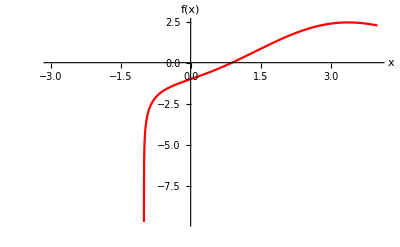

```mathematica
f[x_]=Log[1+x]-Cos[x]
g[x_]=D[f[x],x]
g[x]
FindRoot[f[x], {x,4}]
p=0;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<13,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Root after ", 13, " iterations is ", NumberForm[p1,6]];
Plot[f[x], {x,-3,4}, PlotStyle->{Red}, AxesLabel-> {"x", "f(x)"}]
```

## b) Find root of f(x) = x^2-2 using newton method

```mathematica
ClearAll
```

ClearAll

2 x

{x→1.41421}

1.5

i | pi | f[pi]
0 | 1 | -1
1 | 1.5 | 0.25
2 | 1.41667 | 0.00694444
3 | 1.41422 | 6.0073×10^-6
4 | 1.41421 | 4.51061×10^-12
5 | 1.41421 | 4.44089×10^-16
6 | 1.41421 | -4.44089×10^-16
7 | 1.41421 | 4.44089×10^-16
8 | 1.41421 | -4.44089×10^-16
9 | 1.41421 | 4.44089×10^-16
10 | 1.41421 | -4.44089×10^-16
11 | 1.41421 | 4.44089×10^-16
12 | 1.41421 | -4.44089×10^-16
13 | 1.41421 | 4.44089×10^-16
14 | 1.41421 | -4.44089×10^-16
15 | 1.41421 | 4.44089×10^-16

Root after 15 iterations is 1.41421

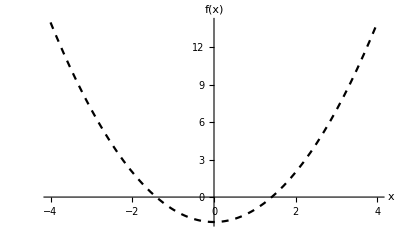

```mathematica
f[x_]=x^2-2;
g[x_]=D[f[x],x]
FindRoot[f[x], {x,4}]
p=1;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<15,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Root after ", 15, " iterations is ", NumberForm[p1,6]];
Plot[f[x], {x,-4,4}, PlotStyle->{Black, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

## Ques 3 : Find the root of the function f(x)=tan(πx)-x-6 by Newton Raphson Method such that f(x_n)>0.0001.

```mathematica
ClearAll
```

ClearAll

-2+x^2

2 x

2 x

{x→1.41421}

1.43333

i | pi | f[pi]
0 | 1.2 | -0.56
1 | 1.43333 | 0.0544444
2 | 1.41434 | 0.000360705
3 | 1.41421 | 1.62606×10^-8

Approximate Root is 1.41421

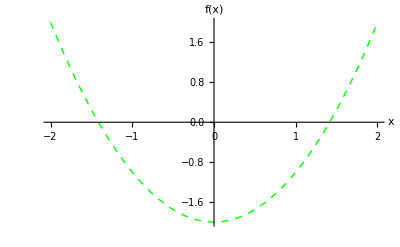

```mathematica
f[x_]=x^2-2
g[x_]=D[f[x],x]
g[x]

FindRoot[f[x], {x,1}]
p=1.2;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0001,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Approximate Root is ", NumberForm[p1,6]];
Plot[f[x], {x,-2,2}, PlotStyle->{Green, Thick, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

## Ques 4 : Perform 10 iterations to find a root of the following equations : - Tan(πx)-x=0 starting from p_0=0.

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]=Tan[πx]-x;
g[x_]=D[f[x],x]
g[x]
```

-1

-1

{x→7.07107}

25.5

i | pi | f[pi]
0 | 1 | -49
1 | 25.5 | 600.25
2 | 13.7304 | 138.524
3 | 8.68597 | 25.4462
4 | 7.22119 | 2.14559
5 | 7.07263 | 0.0220707
6 | 7.07107 | 2.43451×10^-6
7 | 7.07107 | 2.84217×10^-14
8 | 7.07107 | 7.10543×10^-15
9 | 7.07107 | -7.10543×10^-15
10 | 7.07107 | 7.10543×10^-15

Approximate Root is 7.07107

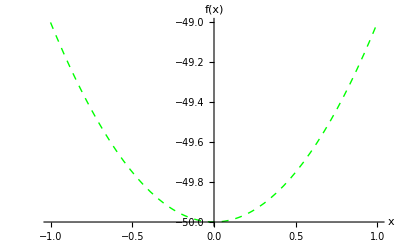

```mathematica
FindRoot[f[x], {x,1}]
p=1;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<10,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Approximate Root is ", NumberForm[p1,6]];
Plot[f[x], {x,-1,1}, PlotStyle->{Green, Thick, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

## Ques 5 : Perform 10 iterations to find a root of the following equations : x^7-90=0

```mathematica
ClearAll
```

ClearAll

7 x^6

{x→1.90186}

13.7143

i | pi | f[pi]
0 | 1 | -89
1 | 13.7143 | 9.12456×10^7
2 | 11.7551 | 3.10159×10^7
3 | 10.0758 | 1.05428×10^7
4 | 8.63642 | 3.58365×10^6
5 | 7.40268 | 1.21812×10^6
6 | 6.34523 | 414035.
7 | 5.43896 | 140714.
8 | 4.66247 | 47807.2
9 | 3.99765 | 16226.8
10 | 3.42971 | 5492.14

Root after 10 iterations is 3.42971

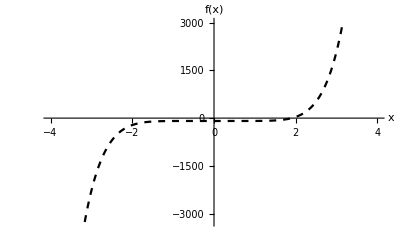

```mathematica
f[x_]=x^7-90;
g[x_]=D[f[x],x]
FindRoot[f[x], {x,4}]
p=1;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[i<10,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Root after ", 10, " iterations is ", NumberForm[p1,6]];
Plot[f[x], {x,-4,4}, PlotStyle->{Black, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

## Ques 6 : Perform Newton Raphson method to obtain approximate root x_n of the following functions. Stop when f(x_n)<0.0005 > x^2-50 = 0

```mathematica
ClearAll
```

ClearAll

-50+x^2

2 x

2 x

{x→7.07107}

21.4333

i | pi | f[pi]
0 | 1.2 | -48.56
1 | 21.4333 | 409.388
2 | 11.8831 | 91.2075
3 | 8.04537 | 14.728
4 | 7.13006 | 0.837788
5 | 7.07131 | 0.00345161
6 | 7.07107 | 5.95639×10^-8

Approximate Root is 7.07107

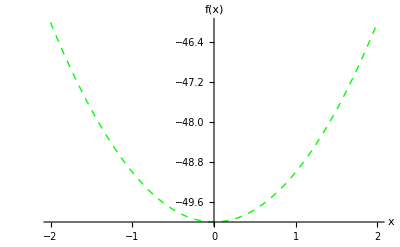

```mathematica
f[x_]=x^2-50
g[x_]=D[f[x],x]
g[x]
FindRoot[f[x], {x,1}]
p=1.2;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0005,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Approximate Root is ", NumberForm[p1,6]];
Plot[f[x], {x,-2,2}, PlotStyle->{Green, Thick, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

## Ques 7 : Perform Newton Raphson method to obtain approximate root x_n of the following functions. Stop when f(x_n)<0.0005 > cos(x) - x e^x = 0 starting from p_0=0.5

```mathematica
f[x_]=Cos[x]-x*e^x
g[x_]=D[f[x],x]
FindRoot[f[x], {x,1}]
p=1;
p1=N[p-(f[p]/g[p])]
i=0;
If[g[p]==0,
Print["We cannot find the root in the given interval"];]
OutputDetails={{i,p,f[p]}};
While[Abs[f[p]]>0.0005,
	i++;
p1=N[p-(f[p]/g[p])];
	OutputDetails=Append[OutputDetails, {i, p1, f[p1]}];
p=p1];
Print[NumberForm[TableForm[OutputDetails, TableHeadings->{None, {"i", "pi", "f[pi]"}}], 6]];
Print["Approximate Root is ", NumberForm[p1,6]];
Plot[f[x], {x,-2,2}, PlotStyle->{Green, Thick, Dashed}, AxesLabel-> {"x", "f(x)"}]
```

-e^x x+Cos[x]

-e^x-e^x x Log[e]-Sin[x]

FindRoot::nlnum: The function value {0.540302-1. e^1.} is not a list of numbers with dimensions {1} at {x} = {1.}.

FindRoot[f[x],{x,1}]

1.-(1. (0.540302-1. e))/(-0.841471-1. e-1. e Log[e])

If[-e-e Log[e]-Sin[1]==0,Print[We cannot find the root in the given interval];]

i | pi | f[pi]
0 | 1 | -e+Cos[1]

Approximate Root is 1.-(1. (0.540302-1. e))/(-0.841471-1. e-1. e Log[e])

-Graphics-